# Study of the bound states

We set     . The branch cut is x ∈[-1,1].

- GF using the variable z

```mathematica
G0ii[ϵ0_,V_,z_]:=1/(2Abs[V]Sign[z-ϵ0]Sqrt[((z-ϵ0)/(2Abs[V]))^2-1]);
G0ij[i_,j_,ϵ0_,V_,z_]:=1/(2Abs[V]Sign[z-ϵ0]Sqrt[((z-ϵ0)/(2Abs[V]))^2-1])(-(z-ϵ0)/(2Abs[V])+Sign[z-ϵ0]Sqrt[((z-ϵ0)/(2Abs[V]))^2-1])^Abs[i-j];
```

```mathematica
G0lm[i_,j_,ϵ0_,V_,z_,ϵ1_,ϵ2_,l1_,l2_]:=G0ij[i,j,ϵ0,V,z]+(ϵ1 G0ij[i,l1,ϵ0,V,z]G0ij[l1,j,ϵ0,V,z])/(1-ϵ1 G0ii[ϵ0,V,z])+(ϵ2(G0ij[i,l2,ϵ0,V,z]+ϵ1/(1-ϵ1 G0ii[ϵ0,V,z])G0ij[i,l1,ϵ0,V,z]G0ij[l1,l2,ϵ0,V,z])(G0ij[l2,j,ϵ0,V,z]+ϵ1/(1-ϵ1 G0ii[ϵ0,V,z])G0ij[l2,l1,ϵ0,V,z]G0ij[l1,j,ϵ0,V,z]))/(1-ϵ2 (G0ij[l2,l2,ϵ0,V,z]+ϵ1/(1-ϵ1 G0ii[ϵ0,V,z])G0ij[l1,l2,ϵ0,V,z]^2) )
```

```mathematica
G[i_,j_,z_,ϵ0_,V_,ϵ1_,ϵ2_,ϵ3_,l1_,l2_,l3_]:=G0lm[i,j,ϵ0,V,z,ϵ1,ϵ2,l1,l2]+(ϵ3 G0lm[i,l3,ϵ0,V,z,ϵ1,ϵ2,l1,l2]G0lm[l3,j,ϵ0,V,z,ϵ1,ϵ2,l1,l2])/(1-ϵ3 G0lm[l3,l3,ϵ0,V,z,ϵ1,ϵ2,l1,l2])
```

```mathematica
flmn[ϵ0_,V_,z_]:=(1-ϵ1 G0ii[ϵ0,V,z])(1-ϵ2 G0ii[ϵ0,V,z])(1-ϵ3 G0ii[ϵ0,V,z])-(1-ϵ1 G0ii[ϵ0,V,z])ϵ2 ϵ3 G0ij[l2,l3,ϵ0,V,z]G0ij[l3,l2,ϵ0,V,z]-(1-ϵ2 G0ii[ϵ0,V,z])ϵ1 ϵ3 G0ij[l1,l3,ϵ0,V,z]G0ij[l3,l1,ϵ0,V,z]-(1-ϵ3 G0ii[ϵ0,V,z])ϵ2 ϵ1 G0ij[l2,l1,ϵ0,V,z]G0ij[l1,l2,ϵ0,V,z]- ϵ1 ϵ2 ϵ3 G0ij[l1,l2,ϵ0,V,z]G0ij[l2,l3,ϵ0,V,z] G0ij[l1,l3,ϵ0,V,z]-ϵ1 ϵ2 ϵ3 G0ij[l2,l1,ϵ0,V,z]G0ij[l3,l2,ϵ0,V,z] G0ij[l3,l1,ϵ0,V,z];
```

- GF using the variable x

```mathematica
G0iix[V_,x_]:=1/(2Abs[V]Sign[x]Sqrt[x^2-1]);
G0ijx[i_,j_,V_,x_]:=1/(2Abs[V]Sign[x]Sqrt[x^2-1])(-x+Sign[x]Sqrt[x^2-1])^Abs[i-j];
```

```mathematica
G0lmx[i_,j_,V_,x_,ϵ1_,ϵ2_,l1_,l2_]:=G0ijx[i,j,V,x]+(ϵ1 G0ijx[i,l1,V,x]G0ijx[l1,j,V,x])/(1-ϵ1 G0iix[V,x])+(ϵ2(G0ijx[i,l2,V,x]+ϵ1/(1-ϵ1 G0iix[V,x])G0ijx[i,l1,V,x]G0ijx[l1,l2,V,x])(G0ijx[l2,j,V,x]+ϵ1/(1-ϵ1 G0iix[V,x])G0ijx[l2,l1,V,x]G0ijx[l1,j,V,x]))/(1-ϵ2 (G0ijx[l2,l2,V,x]+ϵ1/(1-ϵ1 G0iix[V,x])G0ijx[l1,l2,V,x]^2) )
```

```mathematica
Gx[i_,j_,V_,x_,ϵ1_,ϵ2_,ϵ3_,l1_,l2_,l3_]:=G0lmx[i,j,V,x,ϵ1,ϵ2,l1,l2]+(ϵ3 G0lmx[i,l3,V,x,ϵ1,ϵ2,l1,l2]G0lmx[l3,j,V,x,ϵ1,ϵ2,l1,l2])/(1-ϵ3 G0lmx[l3,l3,V,x,ϵ1,ϵ2,l1,l2])
```

```mathematica
flmnx[V_,x_]:=(1-ϵ1 G0iix[V,x])(1-ϵ2 G0iix[V,x])(1-ϵ3 G0iix[V,x])-(1-ϵ1 G0iix[V,x])ϵ2 ϵ3 G0ijx[l2,l3,V,x]G0ijx[l3,l2,V,x]-(1-ϵ2 G0iix[V,x])ϵ1 ϵ3 G0ijx[l1,l3,V,x]G0ijx[l3,l1,V,x]-(1-ϵ3 G0iix[V,x])ϵ2 ϵ1 G0ijx[l2,l1,V,x]G0ijx[l1,l2,V,x]- ϵ1 ϵ2 ϵ3 G0ijx[l1,l2,V,x]G0ijx[l2,l3,V,x] G0ijx[l1,l3,V,x]-ϵ1 ϵ2 ϵ3 G0ijx[l2,l1,V,x]G0ijx[l3,l2,V,x] G0ijx[l3,l1,V,x];
```

```mathematica
ϵ1=ϵ;
ϵ2=ϵ;
ϵ3=ϵ;
l1=1;
l2=l1+d;
l3=l2+d;
V=.;
d=.;
V=1;
FullSimplify[flmnx[V,x],{x<-1,d>0,V>0}]
```

(-8 √(-1+x^2)+4 x^2 (2 √(-1+x^2)+3 ϵ)+ϵ (-12-(-1+(-x-√(-1+x^2))^(2 d)) ϵ (2 √(-1+x^2) (3+(-x-√(-1+x^2))^(2 d))+ϵ-(-x-√(-1+x^2))^(2 d) ϵ)))/(8 (-1+x^2)^(3/2))

```mathematica
f[x_,ϵ_,d_]:=-8 √(-1+x^2)+4 x^2 (2 √(-1+x^2)+3 ϵ)+ϵ (-12-(-1+(-x-√(-1+x^2))^(2 d)) ϵ (2 √(-1+x^2) (3+(-x-√(-1+x^2))^(2 d))+ϵ-(-x-√(-1+x^2))^(2 d) ϵ))
```

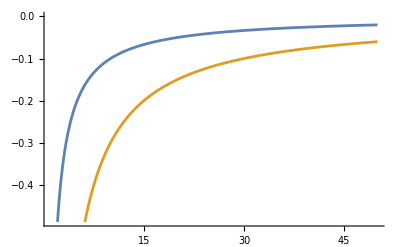

```mathematica
a=Plot[{-1/d,-3/d},{d,1,50}]
```

```mathematica
FullSimplify[flmn[ϵ0,V,z],{d>1∧V>0∧z<ϵ0-2V}]
```

1/((-4 V^2+(z-ϵ0)^2)^(3/2))(-4 V^2 (3 ϵ+√(-4 V^2+(z-ϵ0)^2))+z^2 √(-4 V^2+(z-ϵ0)^2)+3 ϵ^2 √(-4 V^2+(z-ϵ0)^2)+ϵ (ϵ^2+3 (z-ϵ0)^2)-2^(1-2 d) ϵ^3 (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(2 d)-2^(1-2 d) ϵ^2 √(-4 V^2+(z-ϵ0)^2) (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(2 d)+16^-d ϵ^3 (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(4 d)-16^-d ϵ^2 √(-4 V^2+(z-ϵ0)^2) (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(4 d)-2 z √(-4 V^2+(z-ϵ0)^2) ϵ0+√(-4 V^2+(z-ϵ0)^2) ϵ0^2)

```mathematica
g[ϵ0_,V_,z_,ϵ_,d_]:=(-4 V^2 (3 ϵ+√(-4 V^2+(z-ϵ0)^2))+z^2 √(-4 V^2+(z-ϵ0)^2)+3 ϵ^2 √(-4 V^2+(z-ϵ0)^2)+ϵ (ϵ^2+3 (z-ϵ0)^2)-2^(1-2 d) ϵ^3 (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(2 d)-2^(1-2 d) ϵ^2 √(-4 V^2+(z-ϵ0)^2) (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(2 d)+16^-d ϵ^3 (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(4 d)-16^-d ϵ^2 √(-4 V^2+(z-ϵ0)^2) (-(z+√(-4 V^2+(z-ϵ0)^2)-ϵ0)/V)^(4 d)-2 z √(-4 V^2+(z-ϵ0)^2) ϵ0+√(-4 V^2+(z-ϵ0)^2) ϵ0^2)
```

```mathematica
g[ϵ0,V,z,ϵ,d]/.{z->x+ϵ0}//FullSimplify
```

-4 √(-4+x^2)+x^2 (√(-4+x^2)+3 ϵ)+ϵ (-12+4^(-2 d) (4^d-(-x-√(-4+x^2))^(2 d)) ϵ (√(-4+x^2) (3 4^d+(-x-√(-4+x^2))^(2 d))+(4^d-(-x-√(-4+x^2))^(2 d)) ϵ))

```mathematica
Solve[(-x-√(-4+x^2))^(2 d)==a,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1/2 a^(-1/2/d) (4+a^(1/d))}}

```mathematica
-4 √(-4+x^2)+x^2 (√(-4+x^2)+3 ϵ)+ϵ (-12+4^(-2 d) (4^d-(-x-√(-4+x^2))^(2 d)) ϵ (√(-4+x^2) (3 4^d+(-x-√(-4+x^2))^(2 d))+(4^d-(-x-√(-4+x^2))^(2 d)) ϵ))/.{x->-1/2 a^(-1/2/d) (4+a^(1/d))}//FullSimplify
```

-2 √(a^(-1/d) (-4+a^(1/d))^2)+1/8 a^(-1/d) (4+a^(1/d))^2 (√(a^(-1/d) (-4+a^(1/d))^2)+6 ϵ)+ϵ (-12+2^(-1-8 d) (16^d-(-√(a^(-1/d) (-4+a^(1/d))^2)+a^(-1/2/d) (4+a^(1/d)))^(2 d)) ϵ (√(a^(-1/d) (-4+a^(1/d))^2) (3 16^d+(-√(a^(-1/d) (-4+a^(1/d))^2)+a^(-1/2/d) (4+a^(1/d)))^(2 d))+2 (16^d-(-√(a^(-1/d) (-4+a^(1/d))^2)+a^(-1/2/d) (4+a^(1/d)))^(2 d)) ϵ))

```mathematica
s=Solve[{g[ϵ0,1,z,ϵ,1]==0.∧z<ϵ0-2∧ϵ<0},z,Reals]
```

{{z→ConditionalExpression[(1+ϵ^2+ϵ ϵ0)/ϵ, -3<ϵ<-1||ϵ<-3]},{z→ConditionalExpression[Root[-4+3 ϵ^2-ϵ^4+4 ϵ ϵ0-3 ϵ^3 ϵ0+ϵ0^2-3 ϵ^2 ϵ0^2-ϵ ϵ0^3+(-4 ϵ+3 ϵ^3-2 ϵ0+6 ϵ^2 ϵ0+3 ϵ ϵ0^2) #1+(1-3 ϵ^2-3 ϵ ϵ0) #1^2+ϵ #1^3&,1], -3<ϵ<-1||-1<ϵ<0||ϵ<-3]},{z→ConditionalExpression[Root[-4+3 ϵ^2-ϵ^4+4 ϵ ϵ0-3 ϵ^3 ϵ0+ϵ0^2-3 ϵ^2 ϵ0^2-ϵ ϵ0^3+(-4 ϵ+3 ϵ^3-2 ϵ0+6 ϵ^2 ϵ0+3 ϵ ϵ0^2) #1+(1-3 ϵ^2-3 ϵ ϵ0) #1^2+ϵ #1^3&,3], ϵ<-3]}}

```mathematica
list2={};
list3={};
ϵinc=0.001;

For[d=50,d>=1,d--,
If[Length[list2]==0,ϵ=0.,ϵ=list2[[-1]]];
While[True,
sol=NSolve[{ff[u,ϵ,d]==0.,0<u<1},u,Reals];
If[Length[sol]>=2,Break[]];
ϵ-=ϵinc;
];
AppendTo[list2,ϵ];
If[Length[list3]==0,ϵ=list2[[-1]],ϵ=list3[[-1]]];
While[True,
sol=NSolve[{ff[u,ϵ,d]==0.,0<u<1},u,Reals];
If[Length[sol]>=3,Break[]];
ϵ-=ϵinc;
];
AppendTo[list3,ϵ];
]

Reverse[list2]
Reverse[list3]
```

{-0.998,-0.499,-0.329,-0.251,-0.201,-0.164,-0.143,-0.126,-0.112,-0.101,-0.09,-0.08,-0.077,-0.072,-0.061,-0.061,-0.059,-0.055,-0.048,-0.048,-0.048,-0.046,-0.044,-0.041,-0.039,-0.039,-0.038,-0.036,-0.035,-0.033,-0.033,-0.032,-0.031,-0.028,-0.028,-0.027,-0.027,-0.026,-0.026,-0.026,-0.025,-0.024,-0.024,-0.023,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021}

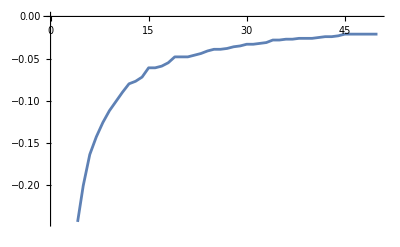

```mathematica
{-0.9980000000000008,-0.4990000000000004,-0.32900000000000024,-0.25100000000000017,-0.20100000000000015,-0.16400000000000012,-0.1430000000000001,-0.12600000000000008,-0.11200000000000009,-0.10100000000000008,-0.09000000000000007,-0.08000000000000006,-0.07700000000000005,-0.07200000000000005,-0.06100000000000005,-0.06100000000000005,-0.059000000000000045,-0.05500000000000004,-0.048000000000000036,-0.048000000000000036,-0.048000000000000036,-0.046000000000000034,-0.04400000000000003,-0.04100000000000003,-0.03900000000000003,-0.03900000000000003,-0.03800000000000003,-0.036000000000000025,-0.035000000000000024,-0.03300000000000002,-0.03300000000000002,-0.03200000000000002,-0.03100000000000002,-0.028000000000000018,-0.028000000000000018,-0.027000000000000017,-0.027000000000000017,-0.026000000000000016,-0.026000000000000016,-0.026000000000000016,-0.025000000000000015,-0.024000000000000014,-0.024000000000000014,-0.023000000000000013,-0.02100000000000001,-0.02100000000000001,-0.02100000000000001,-0.02100000000000001,-0.02100000000000001,-0.02100000000000001}
b=ListLinePlot[%]
```

{-2.923,-1.499,-1.001,-0.751,-0.601,-0.501,-0.429,-0.374,-0.332,-0.298,-0.273,-0.251,-0.231,-0.213,-0.201,-0.187,-0.177,-0.167,-0.158,-0.151,-0.143,-0.136,-0.131,-0.124,-0.121,-0.115,-0.111,-0.108,-0.104,-0.099,-0.097,-0.093,-0.091,-0.089,-0.084,-0.084,-0.082,-0.079,-0.077,-0.074,-0.073,-0.071,-0.069,-0.068,-0.067,-0.065,-0.064,-0.062,-0.062,-0.058}

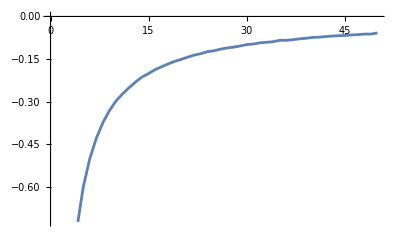

```mathematica
{-2.922999999999789,-1.4989999999999457,-1.0010000000000006,-0.7510000000000006,-0.6010000000000004,-0.5010000000000003,-0.4290000000000003,-0.3740000000000003,-0.33200000000000024,-0.2980000000000002,-0.2730000000000002,-0.25100000000000017,-0.23100000000000018,-0.21300000000000016,-0.20100000000000015,-0.18700000000000014,-0.17700000000000013,-0.16700000000000012,-0.1580000000000001,-0.1510000000000001,-0.1430000000000001,-0.1360000000000001,-0.1310000000000001,-0.1240000000000001,-0.1210000000000001,-0.11500000000000009,-0.11100000000000008,-0.10800000000000008,-0.10400000000000008,-0.09900000000000007,-0.09700000000000007,-0.09300000000000007,-0.09100000000000007,-0.08900000000000007,-0.08400000000000006,-0.08400000000000006,-0.08200000000000006,-0.07900000000000006,-0.07700000000000005,-0.07400000000000005,-0.07300000000000005,-0.07100000000000005,-0.06900000000000005,-0.06800000000000005,-0.06700000000000005,-0.06500000000000004,-0.06400000000000004,-0.06200000000000005,-0.06200000000000005,-0.058000000000000045}
c=ListLinePlot[%]
```

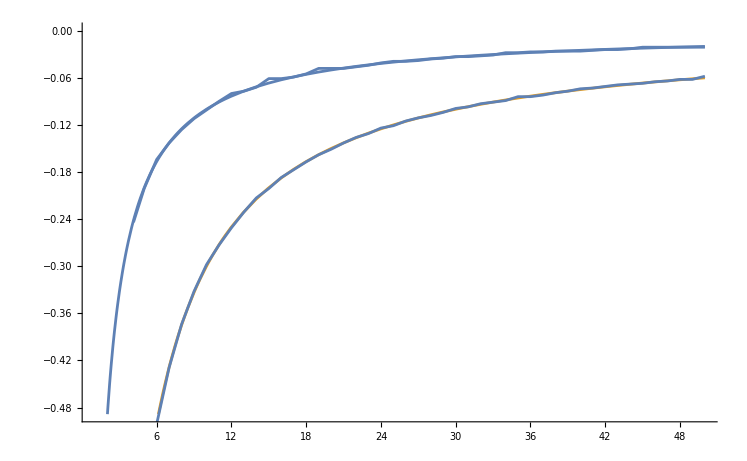

```mathematica
Show[a,b,c]
```